```mathematica
"04:46.0"/.x__:y__.z__ ->x*60+y+z/100
```

Optional::optloose: Optional pattern x__:(y__).(z__) has no enclosing pattern so no optional value can be matched.

60 04:46.0+y+z/100

```mathematica
"04:46.0"/.{x__:y__.z__ ->x*60+y+z/100}
```

Optional::optloose: Optional pattern x__:(y__).(z__) has no enclosing pattern so no optional value can be matched.

60 04:46.0+y+z/100

```mathematica
StringCases["4:46.38",x___~~":"~~y___~~"."~~z___->{x,y,z}]
```

{{4,46,38}}

```mathematica
ToExpression[%][[1]][[1]]*60
```

240

```mathematica
numbers={"4:46.38","4:48.78","5:27.22"}
```

{4:46.38,4:48.78,5:27.22}

```mathematica
StringCases[numbers,x___~~":"~~y___~~"."~~z___->{x,y,z}]
```

{{{4,46,38}},{{4,48,78}},{{5,27,22}}}

```mathematica
Flatten[%,1]
```

{{4,46,38},{4,48,78},{5,27,22}}

```mathematica
times = {"4:46.38","4:48.78","5:27.22","1:23.14","1:31.54","10:52.55","6:47.36","3:53.11","4:12.39","3:27.13","2:24.37","2:45.08","25:50.02","3:41.51","2:47.13","2:22.08","1:40.16","3:12.55","12:23.14","4:12:25","2:33.51","1:17.44","5:33.02","18:23.12","4:29.23","1:40.33","8:02.15","3:12:51","2:46.43","4:13.40","7:32.23","1:57.12","3:10.02","7:22:28","8:50.33","6:55.49","5:33.22","2:56.09","1:44.13","4:14.56","1:32.41","4:27.39","7:15.03", "2:10.37", "3:05.20", "4:02.57", "4:20.48", "2:04.33", "3:55.12", "3:56.49", "2:44.58", "3:11.21", "1:51.17", "3:21.29", "5:58.12", "2:33.11", "4:43.41", "7:11.54"}
```

{4:46.38,4:48.78,5:27.22,1:23.14,1:31.54,10:52.55,6:47.36,3:53.11,4:12.39,3:27.13,2:24.37,2:45.08,25:50.02,3:41.51,2:47.13,2:22.08,1:40.16,3:12.55,12:23.14,4:12:25,2:33.51,1:17.44,5:33.02,18:23.12,4:29.23,1:40.33,8:02.15,3:12:51,2:46.43,4:13.40,7:32.23,1:57.12,3:10.02,7:22:28,8:50.33,6:55.49,5:33.22,2:56.09,1:44.13,4:14.56,1:32.41,4:27.39,7:15.03,2:10.37,3:05.20,4:02.57,4:20.48,2:04.33,3:55.12,3:56.49,2:44.58,3:11.21,1:51.17,3:21.29,5:58.12,2:33.11,4:43.41,7:11.54}

```mathematica
separatedTimes = Flatten[StringCases[times,x___~~":"~~y___~~"."~~z___->{x,y,z}],1]
```

{{4,46,38},{4,48,78},{5,27,22},{1,23,14},{1,31,54},{10,52,55},{6,47,36},{3,53,11},{4,12,39},{3,27,13},{2,24,37},{2,45,08},{25,50,02},{3,41,51},{2,47,13},{2,22,08},{1,40,16},{3,12,55},{12,23,14},{2,33,51},{1,17,44},{5,33,02},{18,23,12},{4,29,23},{1,40,33},{8,02,15},{2,46,43},{4,13,40},{7,32,23},{1,57,12},{3,10,02},{8,50,33},{6,55,49},{5,33,22},{2,56,09},{1,44,13},{4,14,56},{1,32,41},{4,27,39},{7,15,03},{2,10,37},{3,05,20},{4,02,57},{4,20,48},{2,04,33},{3,55,12},{3,56,49},{2,44,58},{3,11,21},{1,51,17},{3,21,29},{5,58,12},{2,33,11},{4,43,41},{7,11,54}}

```mathematica
N/@(ToExpression[#[[1]]]*60+ToExpression[#[[2]]]+ToExpression[#[[3]]]/100&)/@separatedTimes
```

{286.38,288.78,327.22,83.14,91.54,652.55,407.36,233.11,252.39,207.13,144.37,165.08,1550.02,221.51,167.13,142.08,100.16,192.55,743.14,153.51,77.44,333.02,1103.12,269.23,100.33,482.15,166.43,253.4,452.23,117.12,190.02,530.33,415.49,333.22,176.09,104.13,254.56,92.41,267.39,435.03,130.37,185.2,242.57,260.48,124.33,235.12,236.49,164.58,191.21,111.17,201.29,358.12,153.11,283.41,431.54}

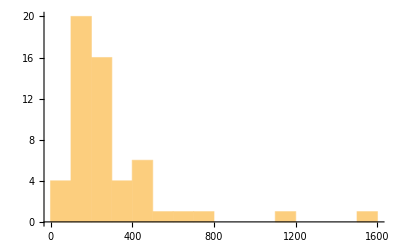

```mathematica
Histogram[%]
```

```mathematica
N/@(ToExpression[#[[1]]]+ToExpression[#[[2]]]/60+ToExpression[#[[3]]]/6000&)/@separatedTimes
```

{4.773,4.813,5.45367,1.38567,1.52567,10.8758,6.78933,3.88517,4.2065,3.45217,2.40617,2.75133,25.8337,3.69183,2.7855,2.368,1.66933,3.20917,12.3857,2.5585,1.29067,5.55033,18.3853,4.48717,1.67217,8.03583,2.77383,4.22333,7.53717,1.952,3.167,8.83883,6.92483,5.55367,2.93483,1.7355,4.24267,1.54017,4.4565,7.2505,2.17283,3.08667,4.04283,4.34133,2.07217,3.91867,3.9415,2.743,3.18683,1.85283,3.35483,5.96867,2.55183,4.7235,7.19233}

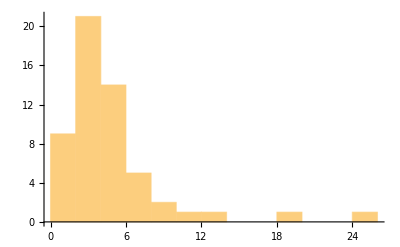

```mathematica
Histogram[%]
```